## Problem 3

```mathematica
ClearAll["Global`*"]
Derive[f_, {x__}] :=D[f[{x}], {{x}}]

(*example*)
f[{x__}]:={x}[[1]]^2+α*{x}[[2]]^2
Derive[Sin, {x}]
```

{{Cos[x]}}

## Problem 4

{0,0}

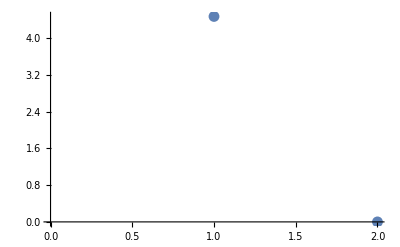

```mathematica
ClearAll["Global`*"]
Derive[f_, {x__}] :=D[f[{x}], {{x}}]
f[{x__}]:={x}[[1]]^2+α*{x}[[2]]^2

α=1;
dfs = Derive[f, {x1, x2}];
x= {{1, 2}};
currentdfs = dfs/.Thread[{x1, x2}->x[[1]]];
TwoNorm={Norm[currentdfs]};

(*This would normally be in a for loop, but it works on first iterate*)
AppendTo[x,x[[-1]]-Inverse[D[dfs, {{x1, x2}}]].currentdfs];
currentdfs = dfs/.Thread[{x1, x2}->x[[-1]]];
AppendTo[TwoNorm,Norm[currentdfs]];

x[[-1]]
ListPlot[TwoNorm]
```

{0,0}

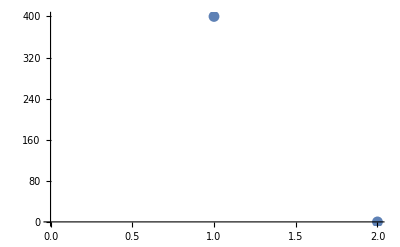

```mathematica
α=100;
dfs = Derive[f, {x1, x2}];
x= {{1, 2}};
currentdfs = dfs/.Thread[{x1, x2}->x[[1]]];
TwoNorm={Norm[currentdfs]};

(*This would normally be in a for loop, but it works on first iterate*)
AppendTo[x,x[[-1]]-Inverse[D[dfs, {{x1, x2}}]].currentdfs];
currentdfs = dfs/.Thread[{x1, x2}->x[[-1]]];
AppendTo[TwoNorm,Norm[currentdfs]];

x[[-1]]
ListPlot[TwoNorm]
```

## Problem 5

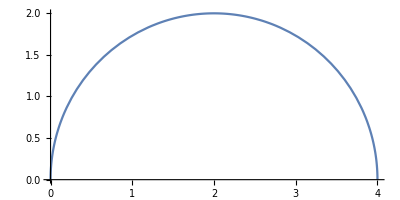

```mathematica
ClearAll["Global`*"]

X = {x[t], y[t], th[t]};
dX =D[X, t];

u1 = 1;
u2 = -1/2;
T = 2*π;
init = Thread[(X/.t->0) == {0,0,π/2}];
eq = Thread [dX == {Cos[th[t]]*u1, Sin[th[t]]*u1, u2}];
sol=NDSolve[Join[init, eq], X, {t, 0, 10}];

xsol=x[t]/.sol[[1]];
ysol = y[t]/.sol[[1]];
ParametricPlot[{xsol, ysol},{t, 0, T}]
```